### Функции плотности вероятности различных распределений

```mathematica
data1=RandomVariate[NormalDistribution[],100000];
```

```mathematica
RandNormal[count_, center_]:=RandomVariate[NormalDistribution[center, 3], count];
```

```mathematica
data1
```

#### Математическое ожидание

```mathematica
Mean[data1]
```

0.00141988

```mathematica
0.0035192907547864404
```

0.00351929

Отсутствие смещения не означает "случайность"

```mathematica
Mean[{0,1,0,1,0,1, 0, 1, 0, 1}]
```

1/2

#### Нормальное распределение

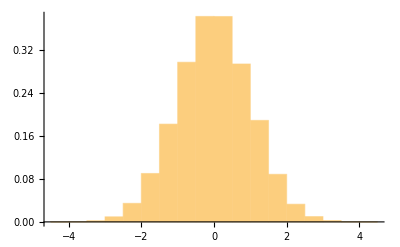

```mathematica
Show[Histogram[data1,Automatic,"ProbabilityDensity"]]
```

```mathematica
Plot[{Table[PDF[NormalDistribution[0,σ],x],{σ,{0.5,0.75,1.5}}]//Evaluate, data1},{x,-4,4},Filling->Axis]
```

$Aborted

#### Логнормальное распределение

```mathematica
data2 = RandomVariate[LogNormalDistribution[0,0.5], 100000]
```

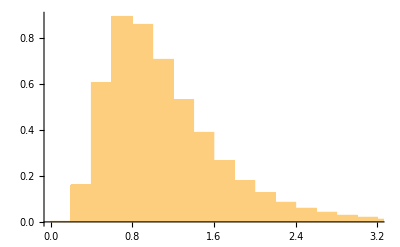

```mathematica
Show[Histogram[data2,Automatic,"ProbabilityDensity"]]
```

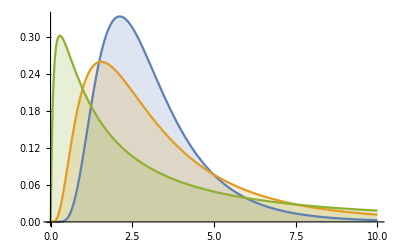

```mathematica
Plot[Table[PDF[LogNormalDistribution[1,σ],x],{σ,{0.5,0.75,1.5}}]//Evaluate,{x,0,10},Filling->Axis, PlotRange->All]
```

#### Распределение Пуассона

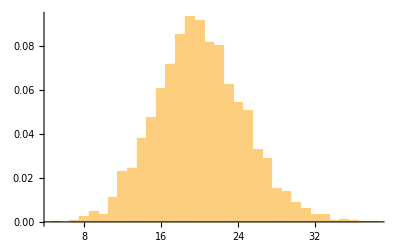

```mathematica
data3=RandomVariate[PoissonDistribution[20],2500];
Show[Histogram[data3,Automatic,"ProbabilityDensity"]]
```

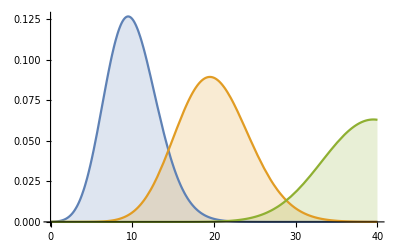

```mathematica
Plot[Table[PDF[PoissonDistribution[mu],x],{mu,{10,20,40}}]//Evaluate,{x,0,40},Filling->Axis]
```

#### Функция плотности и доверительный интервал

```mathematica
pdfNormal=PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
{xl,xr}=Function[α,Quantile[NormalDistribution[],{(1-α)/2.0,(1+α)/2.0}]][Quantity[95, "Percent"]]
```

{-1.95996,1.95996}

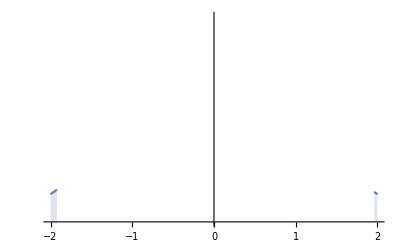

```mathematica
Show[Plot[pdfNormal,{x,-2,2},Filling->Axis,AxesOrigin->{0,0},RegionFunction->(Not[xl<#<xr]&)],Plot[pdf,{x,xl,xr}],PlotRange->{0,0.4},Ticks->{Automatic,None}]
```

### Тестирование ПСЧ методом проверки статистической гипотезы

```mathematica
h1=DistributionFitTest[data1,Automatic,"HypothesisTestData"];
h2=DistributionFitTest[data2,Automatic,"HypothesisTestData"];
```

```mathematica
h1["TestDataTable", All]
```

| Statistic | P-Value
Anderson-Darling | 0.201814 | 0.885498
Baringhaus-Henze | 0.518691 | 0.830527
Cramér-von Mises | 0.0288875 | 0.868209
Jarque-Bera ALM | 1.61273 | 0.446479
Kolmogorov-Smirnov | 0.00164105 | 0.778512
Kuiper | 0.00268901 | 0.887396
Mardia Combined | 1.61273 | 0.446479
Mardia Kurtosis | 0.271618 | 0.785916
Mardia Skewness | 1.53673 | 0.215105
Pearson χ^2 | 205.812 | 0.318834
Watson U^2 | 0.0259548 | 0.877619

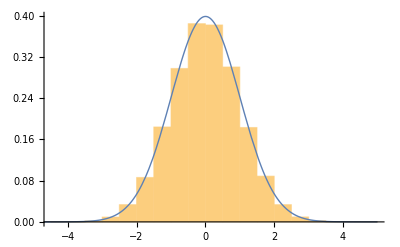

```mathematica
Show[Histogram[data1,Automatic,"ProbabilityDensity"],Plot[PDF[h1["FittedDistribution"],x],{x,-5,5},PlotStyle->Thick]]
```

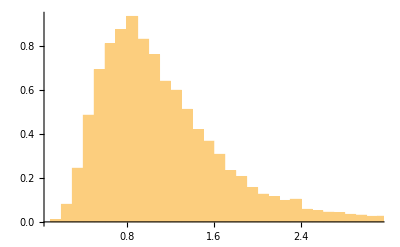

```mathematica
Show[Histogram[data2,Automatic,"ProbabilityDensity"],Plot[PDF[h2["FittedDistribution"],x],{x,0,20},PlotStyle->Thick]]
```

```mathematica
Mod[NextPrime[16497], 4]
NextPrime[13497]
```

3

13499

```mathematica
Mod[16267 ,4]
```

3